3 - 7 Steady-state solutions
Find the steady-state motion of the mass-spring system modeled by the ODE.

3.  y'' + 6 y' + 8 y = 42.5 Cos[2 t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
hog=y''[t]+6 y'[t]+8 y[t]==42.5 Cos[2 t]
nar=DSolve[hog,y[t],t]
```

8 y[t]+6 y'[t]+y''[t]==42.5 Cos[2 t]

{{y[t]→ⅇ^(-4. t) C[1]+ⅇ^(-2. t) C[2]+1.0625 (1. Cos[2. t]+3. Sin[2. t])}}

```mathematica
Expand[1.0624999999999991 (1. Cos[2. t]+3.000000000000002 Sin[2. t])]
```

1.0625 Cos[2. t]+3.1875 Sin[2. t]

1. Above: one section of ‘nar’ is expanded ‘by hand’.

```mathematica
nar/.(1.0624999999999991 (1. Cos[2. t]+3.000000000000002 Sin[2. t]))->1.0624999999999991 Cos[2. t]+3.1874999999999996 Sin[2. t]
```

{{y[t]→ⅇ^(-4. t) C[1]+ⅇ^(-2. t) C[2]+1.0625 Cos[2. t]+3.1875 Sin[2. t]}}

2. Above: expanded section reinserted into ‘nar’. This version matches the text answer, if the two constant coefficients C[1] and C[2] assume a value of zero.

5.  (D^2+D+4.25I)y=22.1Cos[4.5]t

```mathematica
ClearAll["Global`*"]
```

```mathematica
opa=y''[t]+y'[t]+4.25 y[t]==22.1 Cos[4.5 t]
erb=DSolve[opa,y[t],t]
```

4.25 y[t]+y'[t]+y''[t]==22.1 Cos[4.5 t]

{{y[t]→ⅇ^(-0.5 t) C[2] Cos[2. t]+ⅇ^(-0.5 t) C[1] Sin[2. t]-2.125 (1. Cos[2. t] Cos[2.5 t]-0.397647 Cos[2. t] Cos[6.5 t]-0.2 Cos[2.5 t] Sin[2. t]-0.0305882 Cos[6.5 t] Sin[2. t]-0.2 Cos[2. t] Sin[2.5 t]-1. Sin[2. t] Sin[2.5 t]+0.0305882 Cos[2. t] Sin[6.5 t]-0.397647 Sin[2. t] Sin[6.5 t])}}

```mathematica
latch=TrigReduce[erb]
```

{{y[t]→-1.28 ⅇ^(-0.5 t) (-0.78125 C[2] Cos[2. t]+1. ⅇ^(0.5 t) Cos[4.5 t]+4.60786×10^-17 ⅇ^(0.5 t) Cos[8.5 t]-0.78125 C[1] Sin[2. t]-0.28125 ⅇ^(0.5 t) Sin[4.5 t])}}

```mathematica
Simplify[latch]
```

{{y[t]→1. ⅇ^(-0.5 t) C[2] Cos[2. t]-1.28 Cos[4.5 t]-5.89806×10^-17 Cos[8.5 t]+1. ⅇ^(-0.5 t) C[1] Sin[2. t]+0.36 Sin[4.5 t]}}

```mathematica
redondo=Simplify[Chop[latch,10^-16]]
```

{{y[t]→1. ⅇ^(-0.5 t) C[2] Cos[2. t]-1.28 Cos[4.5 t]+1. ⅇ^(-0.5 t) C[1] Sin[2. t]+0.36 Sin[4.5 t]}}

```mathematica
narv=Simplify[redondo/.{C[1]->0,C[2]->0}]
```

{{y[t]→-1.28 Cos[4.5 t]+0.36 Sin[4.5 t]}}

1. The above result matches the text answer.

7.  (4 D^2+12D+9I)y=225-75Sin[3t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
halli=4 y''[t]+12 y'[t]+9 y[t]==225-75 Sin[3 t]
wan=DSolve[halli,y[t],t]
```

9 y[t]+12 y'[t]+4 y''[t]==225-75 Sin[3 t]

{{y[t]→ⅇ^(-3 t/2) C[1]+ⅇ^(-3 t/2) t C[2]+1/3 (75+4 Cos[3 t]+3 Sin[3 t])}}

```mathematica
Simplify[wan]
```

{{y[t]→25+ⅇ^(-3 t/2) C[1]+ⅇ^(-3 t/2) t C[2]+4/3 Cos[3 t]+Sin[3 t]}}

```mathematica
sz=Simplify[wan/.{C[1]->0,C[2]->0}]
```

{{y[t]→25+4/3 Cos[3 t]+Sin[3 t]}}

1. The above result matches the text answer.

8 - 15 Transient solutions
Find the transient motion of the mass-spring system modeled by the ODE.

9.  y'' + 3 y' + 3.25 y = 3 Cos[t] - 1.5 Sin[t]

```mathematica
ClearAll["Global`*"]
```

I ran across a perfect way to do the method of undetermined coefficients in Mathematica, for problems like this, at https://mathematica.stackexchange.com/questions/159382/using-the-method-of-undetermined-coefficients, response of Nasser.

```mathematica
(*returns homogeneous and particular solutions*)hAndp[odeH_,rhs_,y_,x_]:=Module[{wronskian,u1,u2,solH,y1,y2,leadingC},leadingC=Cases[odeH,c_ y''[x]:>c];
leadingC=If[leadingC==={},1,First@leadingC];
solH=(y[x]/.First@DSolve[odeH==0,y[x],x]);
{y1,y2}=solH/.C[1] y1_+C[2] y2_:>{y1,y2};(*basis solutions*)wronskian=Det[{{y1,y2},{D[y1,x],D[y2,x]}}];
u1=-Integrate[y2 rhs/(leadingC*wronskian),x];
u2=Integrate[y1 rhs/(leadingC*wronskian),x];
{solH,Simplify[y1 u1+y2 u2]}];
```

```mathematica
odeH=y''[t]+3. y'[t]+3.25 y[t];
rhs=3. Cos[t]-1.5 Sin[t];
```

```mathematica
{yh,yp}=hAndp[odeH,rhs,y,t]
```

{ⅇ^(-1.5 t) C[2] Cos[1. t]+ⅇ^(-1.5 t) C[1] Sin[1. t],0.3 Cos[t]+0.5 Cos[(1.+0. ⅈ) t]-0.6 Sin[t]+1. Sin[(1.+0. ⅈ) t]}

```mathematica
fullSolution=yh+yp
```

0.3 Cos[t]+ⅇ^(-1.5 t) C[2] Cos[1. t]+0.5 Cos[(1.+0. ⅈ) t]-0.6 Sin[t]+ⅇ^(-1.5 t) C[1] Sin[1. t]+1. Sin[(1.+0. ⅈ) t]

```mathematica
colsol=Collect[fullSolution,ⅇ^(-1.5t)]
```

0.3 Cos[t]+0.5 Cos[(1.+0. ⅈ) t]-0.6 Sin[t]+ⅇ^(-1.5 t) (C[2] Cos[1. t]+C[1] Sin[1. t])+1. Sin[(1.+0. ⅈ) t]

```mathematica
colsolSH=0.8Cos[t]+0.4Sin[t]+ⅇ^(-1.5t)(C[2]Cos[t]+C[1]Sin[t])
```

0.8 Cos[t]+0.4 Sin[t]+ⅇ^(-1.5 t) (C[2] Cos[t]+C[1] Sin[t])

The solution in green above matches the answer in the text. However, I have not been successful so far in checking the answer through differentiation and substitution. Whatever problem the following crude attempt has, it is a big one.

```mathematica
cls[t_]=0.8Cos[t]+0.4Sin[t]+ⅇ^(-1.5t)(Cos[t]+Sin[t])
```

0.8 Cos[t]+0.4 Sin[t]+ⅇ^(-1.5 t) (Cos[t]+Sin[t])

```mathematica
cd[t_]=D[cls,t];
```

```mathematica
cd2[t_]=D[cls,{t,2}];
```

```mathematica
Grid[Table[{cd2[k]+3cd[k]+3.25 cls[k],3 Cos[k]-1.5 Sin[k]},{k,{1,2,ⅇ,3,π}}],Frame->All]
```

3.50072 | 0.3587
0.179901 | -2.61239
-1.86409 | -3.35137
-2.42117 | -3.18166
-2.6292 | -3.

11. (D^2+2I)y=Cos[√2 t]+Sin[√2 t]

```mathematica
eqn=y''[x]-(a*x^6+x^2)*y[x];
sol=DSolve[eqn==0,y,x]
```

```mathematica
ClearAll["Global`*"]
```

I reworked Nasser’s module with t instead of x, in the hope it would show the reason for the difficulty.

```mathematica
(*returns homogeneous and particular solutions*)hAndp[odeH_,rhs_,y_,t_]:=Module[{wronskian,u1,u2,solH,y1,y2,leadingC},leadingC=Cases[odeH,c_ y''[t]:>c];
leadingC=If[leadingC==={},1,First@leadingC];
solH=(y[t]/.First@DSolve[odeH==0,y[t],t]);
{y1,y2}=solH/.C[1] y1_+C[2] y2_:>{y1,y2};(*basis solutions*)wronskian=Det[{{y1,y2},{D[y1,t],D[y2,t]}}];
u1=-Integrate[y2 rhs/(leadingC*wronskian),t];
u2=Integrate[y1 rhs/(leadingC*wronskian),t];
{solH,Simplify[y1 u1+y2 u2]}];
```

```mathematica
odeH=y''[t]+2 y[t];
rhs=Cos[√2 t]+ Sin[√2 t];
```

The module still performs.

```mathematica
{yh,yp}=hAndp[odeH,rhs,y,t]
```

{C[1] Cos[√2 t]+C[2] Sin[√2 t],((√2-4 t) Cos[√2 t]+(√2+4 t) Sin[√2 t])/(8 √2)}

The module comes up with a solution which looks a little like the text answer, but not quite.

```mathematica
fullSolution=yh+yp
```

C[1] Cos[√2 t]+C[2] Sin[√2 t]+((√2-4 t) Cos[√2 t]+(√2+4 t) Sin[√2 t])/(8 √2)

Mathematica doubles down on the suspicious solution by DSolving it directly. This is a forward test, not a back test.

```mathematica
y[t]/.First@DSolve[odeH-rhs==0,y[t],t]
```

C[1] Cos[√2 t]+C[2] Sin[√2 t]+1/(8 √2)(-4 t Cos[√2 t]+√2 Cos[√2 t] Cos[2 √2 t]+4 t Sin[√2 t]-√2 Cos[2 √2 t] Sin[√2 t]+√2 Cos[√2 t] Sin[2 √2 t]+√2 Sin[√2 t] Sin[2 √2 t])

Cutting out the latter part, the ‘tail’, of the proposed solution, which seems to contain the wayward-looking content.

```mathematica
outy=1/(8 √2)(-4 t Cos[√2 t]+√2 Cos[√2 t] Cos[2 √2 t]+4 t Sin[√2 t]-√2 Cos[2 √2 t] Sin[√2 t]+√2 Cos[√2 t] Sin[2 √2 t]+√2 Sin[√2 t] Sin[2 √2 t]);
```

The tail is tested on an integer value.

```mathematica
N[outy/.t->2]
```

0.810144

```mathematica
N[((√2-4 t) Cos[√2 t]+(√2+4 t) Sin[√2 t])/(8 √2)/.t->2]
```

The other version of the tail is also tested.

0.810144

```mathematica
N[(t(Sin[√2 t]-Cos[√2 t]))/(2 √2)/.t->2]
```

The text answer ‘tail’ comes back with a different value.

0.890555

13.  (D^2+I)y=Cos[ω t], ω^2≠1

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*returns homogeneous and particular solutions*)hAndp[odeH_,rhs_,y_,x_]:=Module[{wronskian,u1,u2,solH,y1,y2,leadingC},leadingC=Cases[odeH,c_ y''[x]:>c];
leadingC=If[leadingC==={},1,First@leadingC];
solH=(y[x]/.First@DSolve[odeH==0,y[x],x]);
{y1,y2}=solH/.C[1] y1_+C[2] y2_:>{y1,y2};(*basis solutions*)wronskian=Det[{{y1,y2},{D[y1,x],D[y2,x]}}];
u1=-Integrate[y2 rhs/(leadingC*wronskian),x];
u2=Integrate[y1 rhs/(leadingC*wronskian),x];
{solH,Simplify[y1 u1+y2 u2]}];
```

Oddly, the Mathematica machine objected when the symbol ω was used, but not when the symbol a was used. I couldn’t get accommodation for the Assumptions on a, but it didn’t seem to gum up the works.

```mathematica
odeH=y''[t]+ y[t];
rhs=Cos[a t];
```

```mathematica
{yh,yp}=hAndp[odeH,rhs,y,t]
```

{C[1] Cos[t]+C[2] Sin[t],Cos[a t]/(1-a^2)}

The sum of the two parts equals the text answer.

```mathematica
fullSolution=yh+yp
```

C[1] Cos[t]+Cos[a t]/(1-a^2)+C[2] Sin[t]

A forward checking step is available.

```mathematica
y[t]/.First@DSolve[odeH-rhs==0,y[t],t]
```

C[1] Cos[t]+C[2] Sin[t]+(-Cos[t]^2 Cos[a t]-Cos[a t] Sin[t]^2)/(-1+a^2)

15.  (D^2+4D+8I)y=2Cos[2 t]+Sin[2 t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*returns homogeneous and particular solutions*)hAndp[odeH_,rhs_,y_,x_]:=Module[{wronskian,u1,u2,solH,y1,y2,leadingC},leadingC=Cases[odeH,c_ y''[x]:>c];
leadingC=If[leadingC==={},1,First@leadingC];
solH=(y[x]/.First@DSolve[odeH==0,y[x],x]);
{y1,y2}=solH/.C[1] y1_+C[2] y2_:>{y1,y2};(*basis solutions*)wronskian=Det[{{y1,y2},{D[y1,x],D[y2,x]}}];
u1=-Integrate[y2 rhs/(leadingC*wronskian),x];
u2=Integrate[y1 rhs/(leadingC*wronskian),x];
{solH,Simplify[y1 u1+y2 u2]}];
```

No special circumstances this time. The module runs smoothly.

```mathematica
odeH=y''[t]+ 4y'[t]+8y[t];
rhs=2Cos[2 t]+Sin[2 t];
{yh,yp}=hAndp[odeH,rhs,y,t]
```

{ⅇ^(-2 t) C[2] Cos[2 t]+ⅇ^(-2 t) C[1] Sin[2 t],1/4 Sin[2 t]}

The sum of the two parts matches the answer in the text.

```mathematica
fullSolution=yh+yp
```

ⅇ^(-2 t) C[2] Cos[2 t]+1/4 Sin[2 t]+ⅇ^(-2 t) C[1] Sin[2 t]

The forward check shows agreement with the module output.

```mathematica
y[t]/.First@DSolve[odeH-rhs==0,y[t],t]
```

```mathematica
ⅇ^(-2 t) C[2] Cos[2 t]+ⅇ^(-2 t) C[1] Sin[2 t]+1/8 (-8 Cos[t]^2 Cos[2 t] Sin[t]^2+2 Sin[2 t]+Sin[2 t] Sin[4 t])//FullSimplify
```

1/4 Sin[2 t]+ⅇ^(-2 t) (C[2] Cos[2 t]+C[1] Sin[2 t])

So out of four test problems, the Nasser module performs acceptably on three. A welcome method for those undetermined coefficient situations.

16 - 20 Initial value problems
Find the motion of the mass-spring system modeled by the ODE and the initial conditions. Sketch or graph the solution curve. In addition, sketch or graph the curve of y - y_p to see when the system practically reaches the steady state.

17. (D^2+4I)y=Sin[t]+1/3 Sin[3 t]+1/5 Sin[5 t], y[0]=0,y'[0]=3/35

```mathematica
ClearAll["Global`*"]
```

```mathematica
jolt={y''[t]+4 y[t]==Sin[t]+1/3 Sin[3 t]+1/5 Sin[5 t],y[0]==0,y'[0]==3/35}
holt=DSolve[jolt,y[t],t]
```

{4 y[t]+y''[t]==Sin[t]+1/3 Sin[3 t]+1/5 Sin[5 t],y[0]==0,y'[0]==3/35}

{{y[t]→1/1260(63 Cos[2 t] Sin[t]-644 Cos[2 t] Sin[t]^3+210 Cos[t] Sin[2 t]-126 Cos[3 t] Sin[2 t]-21 Cos[5 t] Sin[2 t]-9 Cos[7 t] Sin[2 t]-77 Cos[2 t] Sin[3 t]+21 Cos[2 t] Sin[5 t]+9 Cos[2 t] Sin[7 t])}}

```mathematica
TrigReduce[holt]
```

{{y[t]→1/105 (35 Sin[t]-7 Sin[3 t]-Sin[5 t])}}

1. Above: This expression matches the text answer.

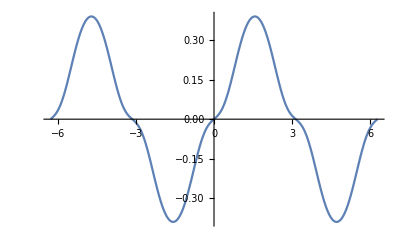

```mathematica
Plot[y[t]/.holt,{t,-2 π,2 π},PlotRange->Automatic]
```

19.  (D^2+2D+2I)y=ⅇ^(-t/2)Sin[1/2 t], y[0]=0, y'[0]=1

```mathematica
ClearAll["Global`*"]
```

```mathematica
num={y''[t]+2 y'[t]+2 y[t]==ⅇ^(-t/2) Sin[1/2 t],y[0]==0,y'[0]==1}
stum=DSolve[num,y[t],t]
```

{2 y[t]+2 y'[t]+y''[t]==ⅇ^(-t/2) Sin[t/2],y[0]==0,y'[0]==1}

{{y[t]→-1/10 ⅇ^-t (-4 Cos[t]+5 ⅇ^(t/2) Cos[t/2] Cos[t]-ⅇ^(t/2) Cos[t] Cos[(3 t)/2]+5 ⅇ^(t/2) Cos[t] Sin[t/2]-8 Sin[t]-5 ⅇ^(t/2) Cos[t/2] Sin[t]+3 ⅇ^(t/2) Cos[(3 t)/2] Sin[t]+5 ⅇ^(t/2) Sin[t/2] Sin[t]-3 ⅇ^(t/2) Cos[t] Sin[(3 t)/2]-ⅇ^(t/2) Sin[t] Sin[(3 t)/2])}}

```mathematica
blum=TrigReduce[stum]
```

{{y[t]→-2/5 ⅇ^-t (ⅇ^(t/2) Cos[t/2]-Cos[t]-2 ⅇ^(t/2) Sin[t/2]-2 Sin[t])}}

```mathematica
rum=Collect[blum,ⅇ^(t/2)]
```

{{y[t]→-2/5 ⅇ^(-t/2) (Cos[t/2]-2 Sin[t/2])-2/5 ⅇ^-t (-Cos[t]-2 Sin[t])}}

1. Above: Marking the first time I used Collect that it worked fairly well.

```mathematica
tum=rum/.(-2/5(Cos[t/2]-2 Sin[t/2]))->(-2/5 Cos[t/2]+4/5 Sin[t/2])
```

{{y[t]→ⅇ^(-t/2) (-2/5 Cos[t/2]+4/5 Sin[t/2])-2/5 ⅇ^-t (-Cos[t]-2 Sin[t])}}

2. Above: I feel confident that using Expand would have messed it up, so I did the distribution by hand. I did only one half of it, leaving the other half for the next step.

```mathematica
zum=tum/.(-2/5 ⅇ^-t (-Cos[t]-2 Sin[t]))->( ⅇ^-t (2/5 Cos[t]+4/5 Sin[t]))
```

{{y[t]→ⅇ^(-t/2) (-2/5 Cos[t/2]+4/5 Sin[t/2])+ⅇ^-t ((2 Cos[t])/5+(4 Sin[t])/5)}}

3. Above: Carrying out the other half of the distribution of constants inside parentheses. At this point the answer matches the text answer, except that rationals are retained in fractional form.

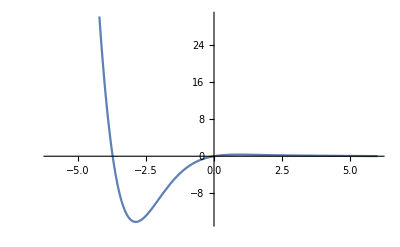

```mathematica
Plot[y[t]/.zum,{t,-6,6},PlotRange->Automatic]
```

21.  Beats. Derive the formula after (12) from (12). Can we have beats in a damped system?

23.  Team experiment. Practical resonance.
(a) Derive, in detail, the crucial formula (16).
(b) By considering (dC*)/dc show that C*(ω_max) increases as c (≤ √(2mk) decreases.
(c) Illustrate practical resonance with an ODE of your own in which you vary c, and sketch or graph corresponding curves as in fig 57.
(d) Take your ODE with c fixed and an input of two terms, one with frequency and the other not. Discuss and sketch or graph the output.
(e) Give other applications (not in the book) in which resonance is important.

```mathematica
ClearAll["Global`*"]
```

After playing with it awhile, I can’t make it look anything like figure 57.

```mathematica
Table[Plot[2/(c √(4 ω^2-c^2)),{ω,0,2},PlotRange->{{0,2},{-2,12}}],{c,0.1,2,0.4}];
```

However I did run across the exact desired plot on the site of Nasser M. Abbasi,
https://12000.org/my_notes/mma_matlab_control/KERNEL2/index.htm#x1-20001.1, at approx 22 percent scroll. Text notes from that site include the following: “Problem: Plot the standard curves showing how the dynamic response R_d changes as r = ω/ω_n changes. Do this for different damping ratio ξ. Also plot the phase angle. These plots are the result of analysis of the response of a second order damped system to a harmonic loading. ω is the forcing frequency and ω_n is the natural frequency of the system.”

Note: I have not yet included the plot of the phase angles.

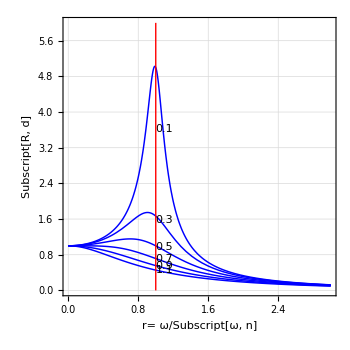

```mathematica
Rd[r_,z_]:=1/Sqrt[(1-r^2)^2+(2 z r)^2];

phase[r_,z_]:=Module[{t},t=ArcTan[(2z r)/(1-r^2)];
If[t<0,t=t+Pi];
180/Pi t];

plotOneZeta[z_,f_]:=Module[{r,p1,p2},p1=Plot[f[r,z],{r,0,3},PlotRange->All,PlotStyle->{Blue,Thickness[0.003]}];
p2=Graphics[Text[z,{1.1,1.1f[1.1,z]}]];
Show[{p1,p2}]];

p1=Graphics[{Red,Line[{{1,0},{1,6}}]}];
p2=Map[plotOneZeta[#,Rd]&,Range[.1,1.2,.2]];

Show[p2,p1,FrameLabel->{{"Subscript[R, d]",None},{"r= ω/Subscript[ω, n]","Dynamics Response vs. Frequency ratio for different ξ"}},Frame->True,GridLines->Automatic,GridLinesStyle->Dashed,ImageSize->350,AspectRatio->1]
```

25.  CAS Experiment. Undamped vibrations.
(a) Solve the initial value problem 
y''+y=Cos[ω t], ω^2≠1, y[0]=0, y'[0]=0.
Show that the solution can be written
y[t]=2/(1-ω^2)Sin[1/2(1+ω)t]Sin[1/2(1-ω)t].
(b) Experiment with the solution by changing ω to see the change of the curves from those for small ω (>0) to beats, to resonance, and to large values of ω (see the figure below).

```mathematica
ClearAll["Global`*"]
```

Part (a). With the green cell below showing true, part (a) is complete.

```mathematica
eqn=y''[t]+y[t]==Cos[ω t]
```

y[t]+y''[t]==Cos[t ω]

```mathematica
sol=DSolve[{eqn,y[0]==0,y'[0]==0},y,t,Assumptions->ω^2≠1]
```

{{y→Function[{t},(Cos[t]-Cos[t]^2 Cos[t ω]-Cos[t ω] Sin[t]^2)/(-1+ω^2)]}}

```mathematica
PossibleZeroQ[(2 Sin[1/2 (1+ω) t] Sin[1/2 (1-ω) t])/(1-ω^2)-(Cos[t]-Cos[t]^2 Cos[t ω]-Cos[t ω] Sin[t]^2)/(-1+ω^2)]
```

True

Part (b). Many possible versions of the solution function can be had. The following three, which resemble the plots in figure 60 in the text, are a good sample.

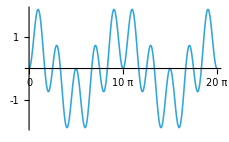
-Graphics-ω=0.2

```mathematica
Labeled[Plot[Table[(2 Sin[1/2 (1+ω) t] Sin[1/2 (1-ω) t])/(1-ω^2),{ω,{0.2}}],{t,0,20π},PlotStyle->{Thickness[0.005],RGBColor[0.2,0.65,0.85]},Ticks->{{0,10Pi,20Pi},{-1,1}},AxesStyle->Thickness[0.004],ImageSize->230],"ω=0.2"]
```

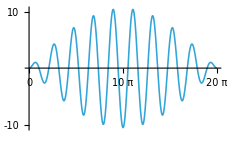
-Graphics-ω=0.9

```mathematica
Labeled[Plot[Table[(2 Sin[1/2 (1+ω) t] Sin[1/2 (1-ω) t])/(1-ω^2),{ω,{0.9}}],{t,0,20π},PlotStyle->{Thickness[0.005],RGBColor[0.2,0.65,0.85]},Ticks->{{0,10Pi,20Pi},{-10,10}},AxesStyle->Thickness[0.004],ImageSize->230],"ω=0.9"]
```

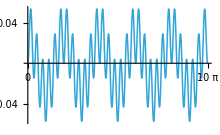
-Graphics-ω=6

```mathematica
Labeled[Plot[Table[(2 Sin[1/2 (1+ω) t] Sin[1/2 (1-ω) t])/(1-ω^2),{ω,{6}}],{t,0,10π},PlotStyle->{Thickness[0.005],RGBColor[0.2,0.65,0.85]},Ticks->{{0,10Pi,20Pi},{-0.04,0.04}},AxesStyle->Thickness[0.004],ImageSize->220],"ω=6"]
```